```mathematica
ψ1[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(σ1 + σ2 + n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n! 2^n))HermiteH[n,(x1+x2)/(√2)];
ψ2[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(σ1 -n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(ⅈ 2θ))^k Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
ψ3[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ (σ2 + n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(-ⅈ 2θ))^k Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
ψ4[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(-n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!2^n))HermiteH[n,(x1+x2)/(√2)];
ψ[n_,x1_,x2_,σ1_,σ2_,θ_]:=-(ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(ⅈ(σ1 + σ2 + n θ))+(ⅇ^(ⅈ 2θ))^k ⅇ^(ⅈ(σ1 -n θ))+(ⅇ^(-ⅈ 2θ))^k ⅇ^(ⅈ (σ2 + n θ))+ⅇ^(ⅈ(-n θ)))Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
(*pr[n_,σ2_,θ_]:=Plot[Abs[ψ[n,0,0,σ1,σ2,θ]]^2,{σ1,-π,π},PlotRange->Full,ImageSize->Scaled[1],AxesLabel->{"σ1","pr[(0,0)]"},LabelStyle->{FontSize->18,FontFamily->"Times", Black}];
cm[n_,σ2_,θ_]:=DensityPlot[Abs[ψ[n,x1,x2,0,σ2,θ]]^2,{x1,-4,4},{x2,-4,4},PlotRange->Full,Mesh->Automatic,ImageSize->Scaled[0.8],AxesLabel->{"x1","x2"},LabelStyle->{FontSize->18,FontFamily->"Times", Black},PlotPoints->30];

g[n_]:=Manipulate[GraphicsGrid[{{pr[n,σ2,π/2],cm[n,σ2,π/2]},{pr[n,σ2,π/3],cm[n,σ2,π/3]},{pr[n,σ2,π/4],cm[n,σ2,π/4]},{pr[n,σ2,π/5],cm[n,σ2,π/5]}}],{σ2,0,2π,Appearance->"Open"}]
g[9]*)
```

```mathematica
ψbefore[n_,x1_,x2_]:=(ⅇ^(-(x1^2+x2^2)/2))/(√(π  n! 2^n))HermiteH[n,(x1+x2)/(√2)];
∫_(-∞)^∞ ∫_(-∞)^∞ Abs[ψbefore[5,x1,x2]]^2 ⅆx1ⅆx2
```

1

```mathematica
(*Export["g9.gif", g[9], "AnimationRepetitions" -> ∞]*)
```

```mathematica
p1=Plot[Abs[ψ[24,(√24)/1,(√24)/1,σ1,0,π/4]]^2/(FindMaximum[Abs[ψ[24,(√24)/1,(√24)/1,x,0,π/4]]^2,{x,π/2}][[1]]),{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P/P_max"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(a)",FontFamily->"Times",FontSize->30]];
p2=Plot[Abs[ψ[24,(√24)/1,(√24)/1,σ1,π,π/4]]^2/(FindMaximum[Abs[ψ[24,(√24)/1,(√24)/1,x,π,π/4]]^2,{x,π}][[1]]),{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P/P_max"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(b)",FontFamily->"Times",FontSize->30]];
Export["24pi4bell.emf",GraphicsRow[{p1,p2}]]
```

24pi4bell.emf

```mathematica
(*p3=Plot[Abs[ψ[8,√8,√8,σ1,0,π/8]]^2,{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(c)",FontFamily->"Times",FontSize->30]];
p4=Plot[Abs[ψ[7,√7,-√7,σ1,0,π/8]]^2,{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(d)",FontFamily->"Times",FontSize->30]];*)
```

```mathematica
(*BellIneq= Import[Export["BellIneq.pdf",GraphicsRow[{p1,p2}],ImageResolution-> 1000,"AllowRasterization"-> False]];
Export["BellIneq.emf",BellIneq[[1]],ImageResolution->1000]*)
```

```mathematica
(*Export["p.emf",p1]*)
```

```mathematica
(*m[n_]:=Manipulate[GraphicsRow[{pr[σ2,2π],cm[σ2,2π]}],{σ2,0,2π,Appearance->"Open"}];
m[4]*)
```

```mathematica
(*DensityPlot[Cos[(x1-x2)/2]^2,{x1,-π,π},{x2,-π,π}]*)
(*manipulate = Manipulate[ContourPlot[Abs[ψ[4,2,2,σ1,σ2,θ]]^2,{σ1,-π,π},{σ2,-π,π},AxesLabel->{"σ1","σ2"}, Mesh->Full,PlotLegends->Placed[Automatic, Right]],{θ,0.1,2π}]*)
```

```mathematica
ψbefore[n_,x1_,x2_]:=(ⅇ^(-(x1^2+x2^2)/2))/(√(π  n!2^n))HermiteH[n,(x1+x2)/(√2)];
```

```mathematica
(*∫_(-∞)^∞ ∫_(-∞)^∞ Abs[ψbefore[6,x1,x2]]^2 ⅆx1ⅆx2*)
```

```mathematica
p5=Plot3D[Abs[ψ1[24,x1,x2,0,0,π/4]]^2,{x1,-6,6},{x2,-6,6},PlotRange->Full, AxesLabel->{"x_1","x_2"},PlotLegends->Automatic,PlotPoints->200,Axes->{True,True,False},LabelStyle->{FontSize->30,FontFamily->"Cambria Math", Black},PlotStyle->Opacity[0.9],ColorFunction->"Rainbow",Mesh->None,PlotLabel-> Style["|ψ_(±±)|^2" ,FontFamily->"Cambria Math",FontSize->30],ImageSize->Scaled[0.8]]
p6=Plot3D[Abs[ψ2[24,x1,x2,0,0,π/4]]^2,{x1,-6,6},{x2,-6,6},PlotRange->Full, AxesLabel->{"x_1","x_2"},PlotLegends->Automatic,PlotPoints->200,Axes->{True,True,False},LabelStyle->{FontSize->30,FontFamily->"Cambria Math", Black},PlotStyle->Opacity[0.9],ColorFunction->"Rainbow",Mesh->None,PlotLabel-> Style["|ψ_(±∓)|^2",FontFamily->"Cambria Math",FontSize->30],ImageSize->Scaled[0.8]]
```

```mathematica
p5plt= Import[Export["p5.pdf",p5,ImageResolution-> 1000,"AllowRasterization"-> False]];
Export["p5.emf",p5plt[[1]],ImageResolution->1000]
p6plt= Import[Export["p6.pdf",p6,ImageResolution-> 1000,"AllowRasterization"-> False]];
Export["p6.emf",p6plt[[1]],ImageResolution->1000]
p7=GraphicsColumn[{p5plt[[1]],p6plt[[1]]}];
p7plt= Import[Export["p7.pdf",p7,ImageResolution-> 1000,"AllowRasterization"-> False]];
Export["p7.emf",p7plt[[1]],ImageResolution->1000]
```

p5.emf

p6.emf

p7.emf

```mathematica
p7=ContourPlot[Abs[ψ3[24,x1,x2,0,0,π/8]]^2,{x1,-6,6},{x2,-6,6},PlotRange->Full, AxesLabel->{"x1","x2"},Mesh->None,PlotPoints->50,Mesh->Full,Axes->True,LabelStyle->{FontSize->15,FontFamily->"Times", Black},Contours->5,GridLines->{{√24}, {√24}},GridLinesStyle->{{Black,Dashed},{Black,Dashed}}];
p8=ContourPlot[Abs[ψ1[24,x1,x2,0,0,π/8]]^2,{x1,-6,6},{x2,-6,6},PlotRange->Full, AxesLabel->{"x1","x2"},Mesh->None,PlotPoints->50,Mesh->Full,Axes->True,LabelStyle->{FontSize->15,FontFamily->"Times", Black},Contours->5,GridLines->{{√24}, {√24}},GridLinesStyle->{{Black,Dashed},{Black,Dashed}}];
Export["24pi81.emf",GraphicsRow[{p7,p8}]]
```

24pi81.emf

```mathematica
(*P=∫_(0.995 √24)^(1.005 √24) ∫_(0.995 √24)^(1.005 √24) Abs[ψ[24,x1,x2,0,0,π/4]]^2 ⅆx1ⅆx2;*)
```

```mathematica
blurryP[n_,σ1_,σ2_,θ_]:=Abs[NIntegrate[ψ[n,x1,x2,σ1,σ2,θ],{x1,0.95 √n,1.05 √n},{x2,.95 √n,1.05 √n}]]^2;
```

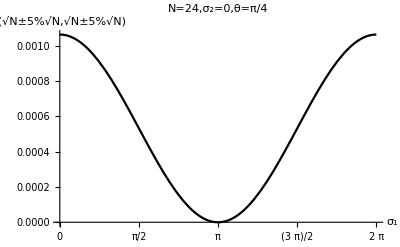

```mathematica
pblurry024=Plot[blurryP[24,σ1,0,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=24,σ_2=0,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

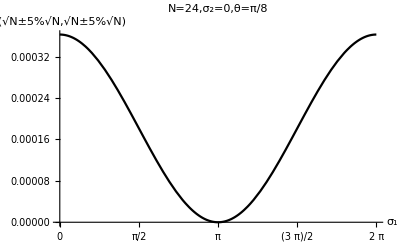

```mathematica
pblurry8024=Plot[blurryP[24,σ1,0,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=24,σ_2=0,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

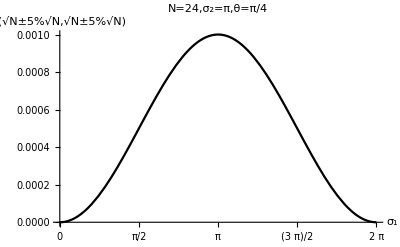

```mathematica
pblurrypi24=Plot[blurryP[24,σ1,π,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=24,σ_2=π,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

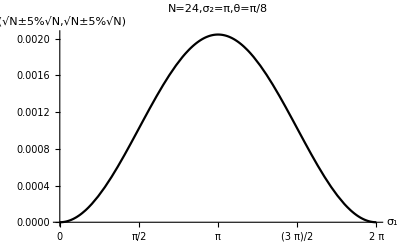

```mathematica
pblurry8pi24=Plot[blurryP[24,σ1,π,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=24,σ_2=π,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

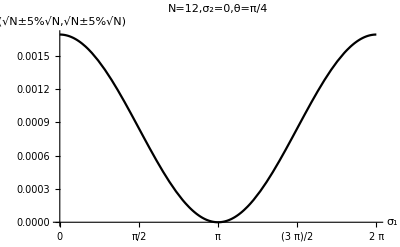

```mathematica
pblurry012=Plot[blurryP[12,σ1,0,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=12,σ_2=0,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

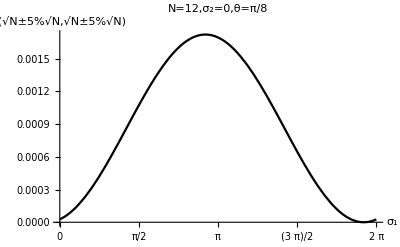

```mathematica
pblurry12012=Plot[blurryP[12,σ1,0,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=12,σ_2=0,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

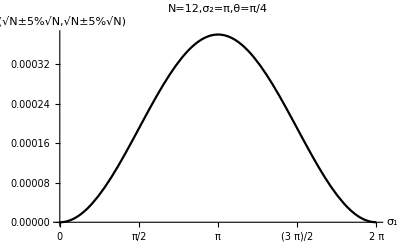

```mathematica
pblurrypi12=Plot[blurryP[12,σ1,π,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=12,σ_2=π,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

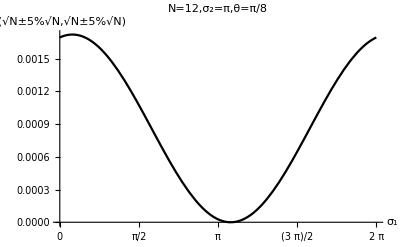

```mathematica
pblurry8pi12=Plot[blurryP[12,σ1,π,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=12,σ_2=π,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

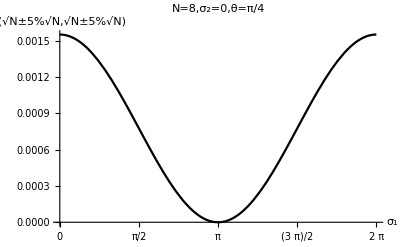

```mathematica
pblurry08=Plot[blurryP[8,σ1,0,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=8,σ_2=0,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

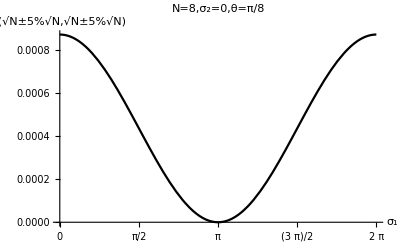

```mathematica
pblurry808=Plot[blurryP[8,σ1,0,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=8,σ_2=0,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

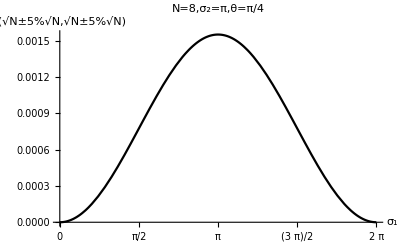

```mathematica
pblurrypi8=Plot[blurryP[8,σ1,π,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=8,σ_2=π,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

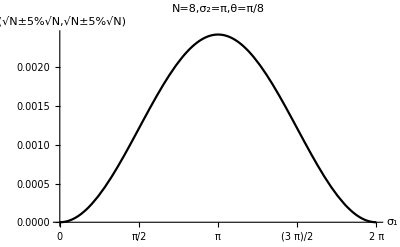

```mathematica
pblurry8pi8=Plot[blurryP[8,σ1,π,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=8,σ_2=π,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

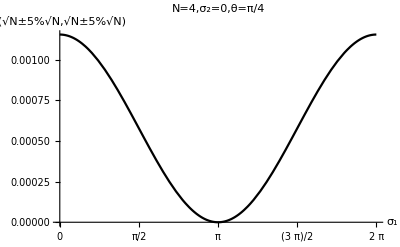

```mathematica
pblurrypi04=Plot[blurryP[4,σ1,0,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=4,σ_2=0,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

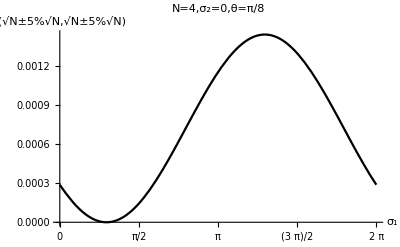

```mathematica
pblurry8pi04=Plot[blurryP[4,σ1,0,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=4,σ_2=0,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

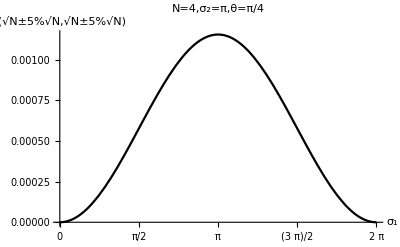

```mathematica
pblurrypi4=Plot[blurryP[4,σ1,π,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=4,σ_2=π,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

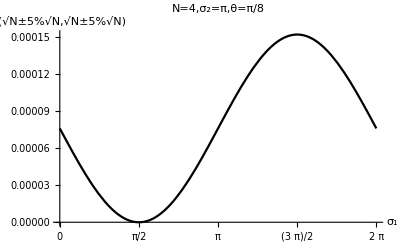

```mathematica
pblurry8pi4=Plot[blurryP[4,σ1,3π/2,π/8],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=4,σ_2=π,θ=π/8",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

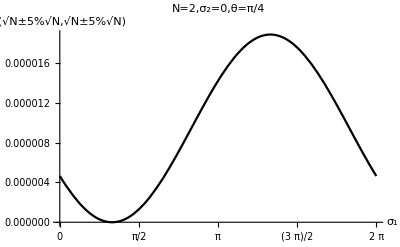

```mathematica
pblurry2pi4=Plot[blurryP[2,σ1,0,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=2,σ_2=0,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

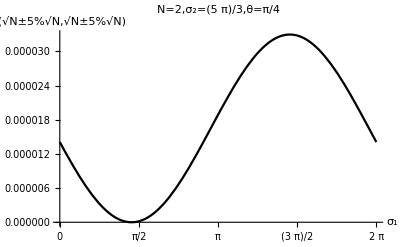

```mathematica
pblurry25pi3pi4=Plot[blurryP[2,σ1,(5π)/3,π/4],{σ1,0,2π},AxesLabel->{"σ_1","P(√N±5%√N,√N±5%√N)"},PlotLabel->"N=2,σ_2=(5  π)/3,θ=π/4",LabelStyle->{FontSize->20,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black]
```

## CHSH Inequality

```mathematica
cpp[n_,x1_,x2_,σ1_,σ2_,θ_]:=ψ1[n,x1,x2,σ1,σ2,θ]+ⅈ^2 ψ2[n,x1,x2,σ1,σ2,θ]+ⅈ^2 ψ3[n,x1,x2,σ1,σ2,θ]+ⅈ^4 ψ4[n,x1,x2,σ1,σ2,θ];
cpm[n_,x1_,x2_,σ1_,σ2_,θ_]:=ⅈ ψ1[n,x1,x2,σ1,σ2,θ]+ⅈ^3 ψ2[n,x1,x2,σ1,σ2,θ]+ⅈ ψ3[n,x1,x2,σ1,σ2,θ]+ⅈ^3 ψ4[n,x1,x2,σ1,σ2,θ];
cmp[n_,x1_,x2_,σ1_,σ2_,θ_]:=ⅈ ψ1[n,x1,x2,σ1,σ2,θ]+ⅈ ψ2[n,x1,x2,σ1,σ2,θ]+ⅈ^3 ψ3[n,x1,x2,σ1,σ2,θ]+ⅈ^3 ψ4[n,x1,x2,σ1,σ2,θ];
cmm[n_,x1_,x2_,σ1_,σ2_,θ_]:=ⅈ^2 ψ1[n,x1,x2,σ1,σ2,θ]+ⅈ^2 ψ2[n,x1,x2,σ1,σ2,θ]+ⅈ^2 ψ3[n,x1,x2,σ1,σ2,θ]+ⅈ^2 ψ4[n,x1,x2,σ1,σ2,θ];
call[n_,x1_,x2_,σ1_,σ2_,θ_]:=√(Abs[cpp[n,x1,x2,σ1,σ2,θ]]^2+Abs[cpm[n,x1,x2,σ1,σ2,θ]]^2+Abs[cmp[n,x1,x2,σ1,σ2,θ]]^2+Abs[cmm[n,x1,x2,σ1,σ2,θ]]^2);
ppp[n_,x1_,x2_,σ1_,σ2_,θ_]:=cpp[n,x1,x2,σ1,σ2,θ]/call[n,x1,x2,σ1,σ2,θ];
ppm[n_,x1_,x2_,σ1_,σ2_,θ_]:=cpm[n,x1,x2,σ1,σ2,θ]/call[n,x1,x2,σ1,σ2,θ];
pmp[n_,x1_,x2_,σ1_,σ2_,θ_]:=cmp[n,x1,x2,σ1,σ2,θ]/call[n,x1,x2,σ1,σ2,θ];
pmm[n_,x1_,x2_,σ1_,σ2_,θ_]:=cmm[n,x1,x2,σ1,σ2,θ]/call[n,x1,x2,σ1,σ2,θ];
Expec[n_,x1_,x2_,σ1_,σ2_,θ_]:=((Abs[cpp[n,x1,x2,σ1,σ2,θ]]^2-Abs[cpm[n,x1,x2,σ1,σ2,θ]]^2-Abs[cmp[n,x1,x2,σ1,σ2,θ]]^2+Abs[cmm[n,x1,x2,σ1,σ2,θ]]^2)/(Abs[cpp[n,x1,x2,σ1,σ2,θ]]^2+Abs[cpm[n,x1,x2,σ1,σ2,θ]]^2+Abs[cmp[n,x1,x2,σ1,σ2,θ]]^2+Abs[cmm[n,x1,x2,σ1,σ2,θ]]^2))
Schsh[n_,x1_,x2_,θ_,a_,b_,aprime_,bprime_]:=Abs[Expec[n,x1,x2,a,b,θ]+Expec[n,x1,x2,a,bprime,θ]+Expec[n,x1,x2,aprime,b,θ]-Expec[n,x1,x2,aprime,bprime,θ]];
```

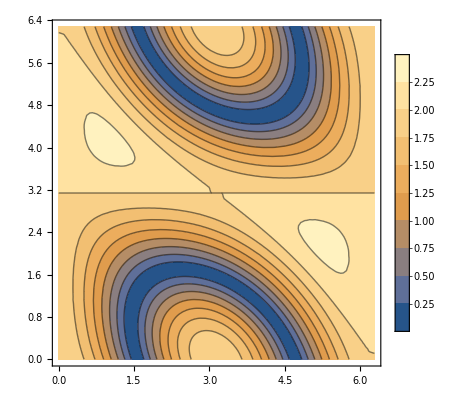

```mathematica
ContourPlot[Schsh[4,2,2,π/4,0,π,aprime,bprime],{aprime,0,2π},{bprime,0,2π},PlotLegends->Automatic]
```

```mathematica
ContourPlot[Schsh[24,√24,√24,π/4,0,π,aprime,bprime],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_a'","σ_b'"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

$Aborted

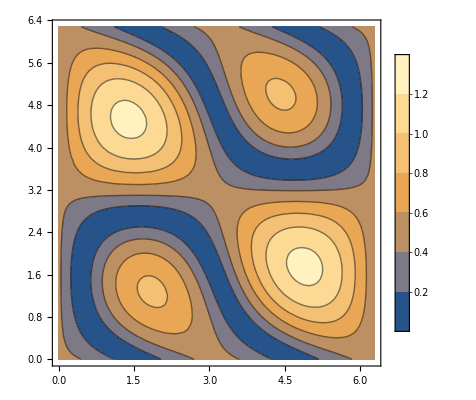

```mathematica
ContourPlot[Schsh[4,2,2,π/8,0,π,aprime,bprime],{aprime,0,2π},{bprime,0,2π},PlotLegends->Automatic]
```

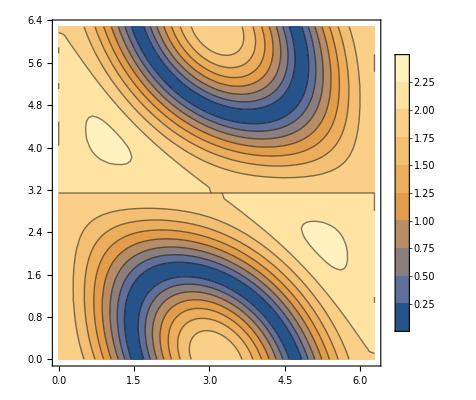

```mathematica
ContourPlot[Schsh[24,√24,√24,π/8,0,π,aprime,bprime],{aprime,0,2π},{bprime,0,2π},PlotLegends->Automatic]
```

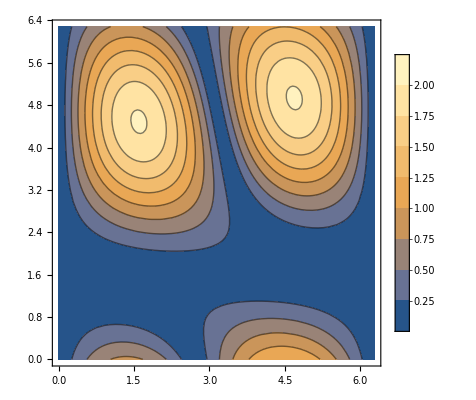

```mathematica
ContourPlot[Schsh[4,2,2,π/8,0,π/2,aprime,bprime],{aprime,0,2π},{bprime,0,2π},PlotLegends->Automatic]
```

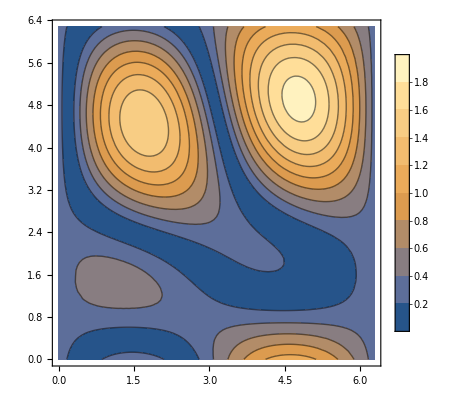

```mathematica
ContourPlot[Schsh[4,2,2,π/8,0,π/4,aprime,bprime],{aprime,0,2π},{bprime,0,2π},PlotLegends->Automatic]
```

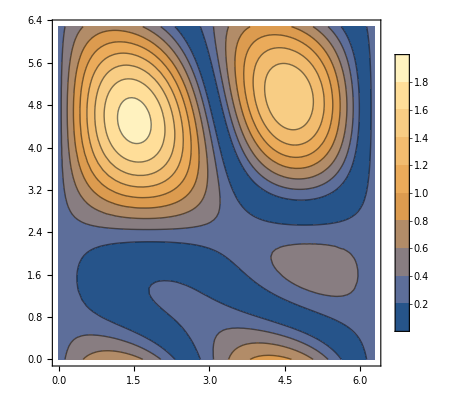

```mathematica
ContourPlot[Schsh[4,2,2,π/8,0,3π/4,aprime,bprime],{aprime,0,2π},{bprime,0,2π},PlotLegends->Automatic]
```

N=2

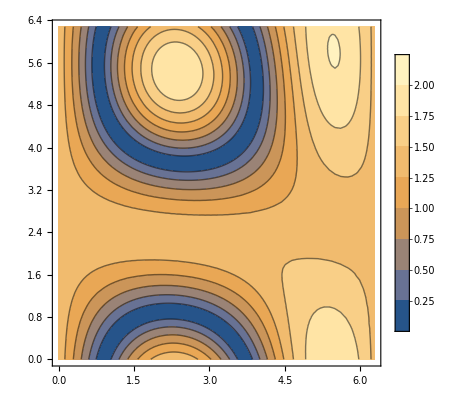

```mathematica
ContourPlot[Schsh[2,√2,√2,π/8,0,3π/4,aprime,bprime],{aprime,0,2π},{bprime,0,2π},PlotLegends->Automatic]
```

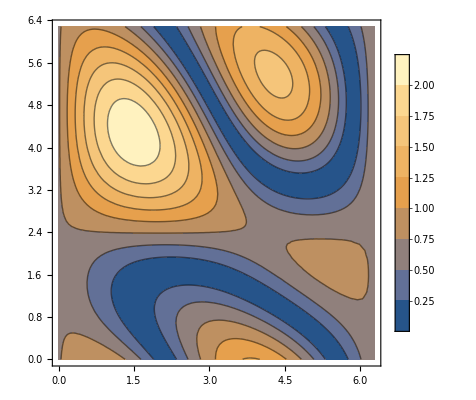

```mathematica
ContourPlot[Schsh[2,√2,√2,π/4,0,3π/4,aprime,bprime],{aprime,0,2π},{bprime,0,2π},PlotLegends->Automatic]
```

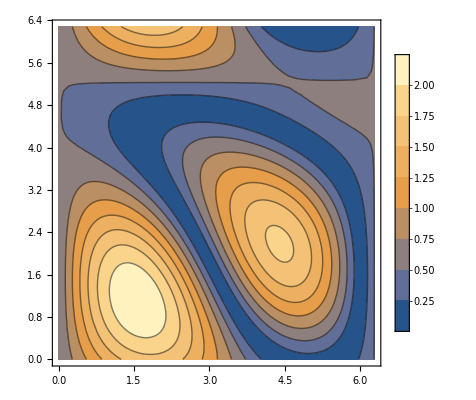

```mathematica
ContourPlot[Schsh[2,√2,√2,π/4,0,5π/3,aprime,bprime],{aprime,0,2π},{bprime,0,2π},PlotLegends->Automatic]
```

```mathematica
S2[2,π/4,0,5π/3,1.6,1]
```

```mathematica
P1=NIntegrate[Abs[cpp[2,x1,x2,0,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

1.2108×10^-7

```mathematica
3.743891846919837*^-10
```

```mathematica
P2=NIntegrate[Abs[cpm[2,x1,x2,0,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.000240244

```mathematica
4.79414478575965*^-6
```

```mathematica
P3=NIntegrate[Abs[cmp[2,x1,x2,0,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.000945749

```mathematica
0.00001888418221593727
```

```mathematica
P4=NIntegrate[Abs[cmm[2,x1,x2,0,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.000705626

```mathematica
0.00001409041181936231
```

```mathematica
Q1=NIntegrate[Abs[cpp[2,x1,x2,0,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.000685947

```mathematica
0.000013697464397229831
```

```mathematica
Q2=NIntegrate[Abs[cpm[2,x1,x2,0,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.000945425

```mathematica
0.00001887763479537359
```

```mathematica
Q3=NIntegrate[Abs[cmp[2,x1,x2,0,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.000259924

```mathematica
5.18709220789213*^-6
```

```mathematica
Q4=NIntegrate[Abs[cmm[2,x1,x2,0,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

4.45148×10^-7

```mathematica
6.921809748374356*^-9
```

```mathematica
R1=NIntegrate[Abs[cpp[2,x1,x2,1.6,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.000121775

```mathematica
2.4248995785812186*^-6
```

```mathematica
R2=NIntegrate[Abs[cpm[2,x1,x2,1.6,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.000118591

```mathematica
2.3696195963631252*^-6
```

```mathematica
R3=NIntegrate[Abs[cmp[2,x1,x2,1.6,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.0016384

```mathematica
0.00003272249345088419
```

```mathematica
R4=NIntegrate[Abs[cmm[2,x1,x2,1.6,5π/3,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.0000129802

```mathematica
2.521005844153865*^-7
```

```mathematica
H1=NIntegrate[Abs[cpp[2,x1,x2,1.6,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.00162409

```mathematica
0.00003243661238532428
```

```mathematica
H2=NIntegrate[Abs[cpm[2,x1,x2,1.6,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

7.28273×10^-6

```mathematica
1.384868072791395*^-7
```

```mathematica
H3=NIntegrate[Abs[cmp[2,x1,x2,1.6,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.000136081

```mathematica
2.7107806441411327*^-6
```

```mathematica
H4=NIntegrate[Abs[cmm[2,x1,x2,1.6,1,π/4]]^2,{x1,0.95 √2,1.05 √2},{x2,0.95 √2,1.05 √2}]
```

0.000124288

```mathematica
2.4832333734993713*^-6
```

```mathematica
ptot=
P1+P2+P3+P4
```

0.00189174

```mathematica
0.000037769113210243924
```

```mathematica
qtot=Q1+Q2+Q3+Q4
```

0.00189174

```mathematica
rtot=R1+R2+R3+R4
```

0.00189174

```mathematica
htot=H1+H2+H3+H4
```

0.00189174

```mathematica
s=(P1-P2-P3+P4)/ptot+(Q1-Q2-Q3+Q4)/qtot+(R1-R2-R3+R4)/rtot-(H1-H2-H3+H4)/htot
```

-2.23416

N=4

```mathematica
P1=NIntegrate[Abs[cpp[4,x1,x2,0,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

1.2107×10^-6

```mathematica
1.2507026699869094*^-42
```

```mathematica
P2=NIntegrate[Abs[cpm[4,x1,x2,0,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.000434008

```mathematica
0.000017326373827819462
```

```mathematica
P3=NIntegrate[Abs[cmp[4,x1,x2,0,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.00228704

```mathematica
0.00009109420291913095
```

```mathematica
P4=NIntegrate[Abs[cmm[4,x1,x2,0,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

1.2107×10^-6

```mathematica
1.2507026699869094*^-42
```

```mathematica
Q1=NIntegrate[Abs[cpp[4,x1,x2,0.9,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.0000830937

```mathematica
3.2780635712314692*^-6
```

```mathematica
Q2=NIntegrate[Abs[cpm[4,x1,x2,0.9,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.000352125

```mathematica
0.000014048310256587999
```

```mathematica
Q3=NIntegrate[Abs[cmp[4,x1,x2,0.9,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.00185457

```mathematica
0.00007385963375266673
```

```mathematica
Q4=NIntegrate[Abs[cmm[4,x1,x2,0.9,π,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.000433677

```mathematica
0.000017234569166464252
```

```mathematica
R1=NIntegrate[Abs[cpp[4,x1,x2,0,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.000471518

```mathematica
0.000018742581362868597
```

```mathematica
R2=NIntegrate[Abs[cpm[4,x1,x2,0,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.00034496

```mathematica
0.000013761482091737498
```

```mathematica
R3=NIntegrate[Abs[cmp[4,x1,x2,0,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.00181673

```mathematica
0.00007235162155626238
```

```mathematica
R4=NIntegrate[Abs[cmm[4,x1,x2,0,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.0000902584

```mathematica
3.564891736081962*^-6
```

```mathematica
H1=NIntegrate[Abs[cpp[4,x1,x2,0.9,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.000763368

```mathematica
0.00003038046353534576
```

```mathematica
H2=NIntegrate[Abs[cpm[4,x1,x2,0.9,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.0000531104

```mathematica
2.1235999192603454*^-6
```

```mathematica
H3=NIntegrate[Abs[cmp[4,x1,x2,0.9,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.0011743

```mathematica
0.00004675723378855245
```

```mathematica
H4=NIntegrate[Abs[cmm[4,x1,x2,0.9,-2.2,π/4]]^2,{x1,0.95 √4,1.05 √4},{x2,0.95 √4,1.05 √4}]
```

0.000732692

```mathematica
0.0000291592795037919
```

```mathematica
ptot=
P1+P2+P3+P4
```

0.00272347

```mathematica
0.00010842057674695042
```

```mathematica
qtot=
Q1+Q2+Q3+Q4
```

0.00272347

```mathematica
0.00010842057674695045
```

```mathematica
rtot=
R1+R2+R3+R4
```

0.00272347

```mathematica
0.00010842057674695043
```

```mathematica
htot=
H1+H2+H3+H4
```

0.00272347

```mathematica
0.00010842057674695046
```

```mathematica
s=(P1-P2-P3+P4)/ptot+(Q1-Q2-Q3+Q4)/qtot+(R1-R2-R3+R4)/rtot-(H1-H2-H3+H4)/htot
```

-2.30483

```mathematica
-2.3084218458183337
```

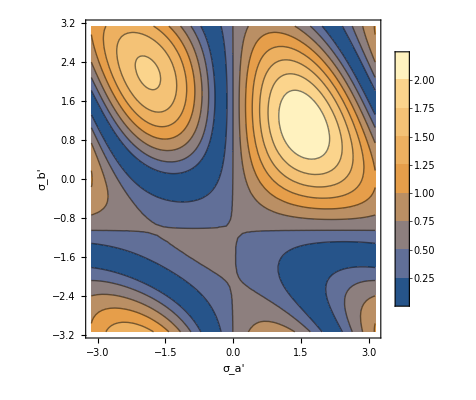

```mathematica
ContourPlot[Schsh[2,√2,√2,π/4,0,5π/3,aprime,bprime],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_a'","σ_b'"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

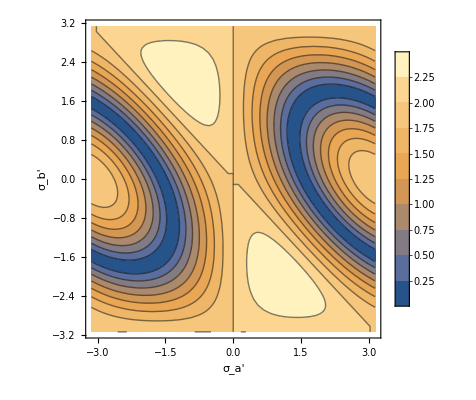

```mathematica
cplt2=ContourPlot[Schsh[24,√24,√24,π/4,0,π,aprime,bprime],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_a'","σ_b'"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

```mathematica
Export["cplt2.emf",cplt2,ImageResolution->800,ImageSize->Scaled[1]]
```

cplt2.emf

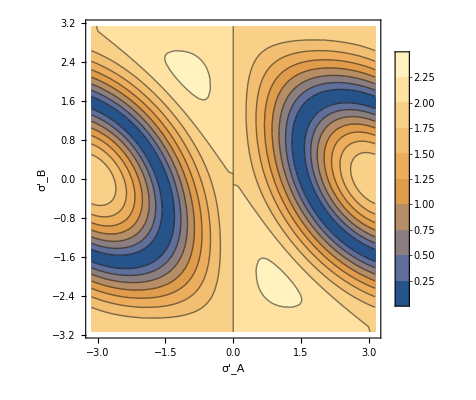

```mathematica
cplt =ContourPlot[Schsh[4,2,2,π/4,0,π,aprime,bprime],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[-Pi,Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

```mathematica
Export["clpt.emf",cplt,ImageResolution->800,ImageSize->Scaled[1]]
```

clpt.emf

```mathematica
ContourPlot[Schsh[4,2,2,π/4,0,π,aprime,bprime],{aprime,0,2π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_a'","σ_b'"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

-Graphics-

```mathematica
ContourPlot[Schsh[2,2,2,π/4,0,π,aprime,bprime],{aprime,0,2π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_a'","σ_b'"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

```mathematica
Expec2[n_,σ1_,σ2_,θ_]:=((Abs[Integrate[cpp[n,x1,x2,σ1,σ2,θ],{x1,0.95 √n,1.05 √n},{x2,0.95 √n,1.05 √n}]]^2-Abs[Integrate[cpm[n,x1,x2,σ1,σ2,θ],{x1,0.95 √n,1.05 √n},{x2,0.95 √n,1.05 √n}]]^2-Abs[Integrate[cmp[n,x1,x2,σ1,σ2,θ],{x1,0.95 √n,1.05 √n},{x2,0.95 √n,1.05 √n}]]^2+Abs[Integrate[cmm[n,x1,x2,σ1,σ2,θ],{x1,0.95 √n,1.05 √n},{x2,0.95 √n,1.05 √n}]]^2)/(Abs[Integrate[cpp[n,x1,x2,σ1,σ2,θ],{x1,0.95 √n,1.05 √n},{x2,0.95 √n,1.05 √n}]]^2+Abs[Integrate[cpm[n,x1,x2,σ1,σ2,θ],{x1,0.95 √n,1.05 √n},{x2,0.95 √n,1.05 √n}]]^2+Abs[Integrate[cmp[n,x1,x2,σ1,σ2,θ],{x1,0.95 √n,1.05 √n},{x2,0.95 √n,1.05 √n}]]^2+Abs[Integrate[cmm[n,x1,x2,σ1,σ2,θ],{x1,0.95 √n,1.05 √n},{x2,0.95 √n,1.05 √n}]]^2));
S2[n_,θ_,a_,b_,aprime_,bprime_]:=Abs[Expec2[n,a,b,θ]+Expec2[n,a,bprime,θ]+Expec2[n,aprime,b,θ]-Expec2[n,aprime,bprime,θ]];
```

```mathematica
(*ContourPlot[S2[4,π/4,0,π,aprime,bprime],{aprime,1-.01,1+0.01},{bprime,-2.5+0.01,-2.5+.01},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_a'","σ_b'"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]*)
```

```mathematica
ContourPlot[S2[4,π/4,0,π,aprime,bprime],{aprime,1-.01,1+0.01},{bprime,-2.5+0.01,-2.5+.01},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ_a'","σ_b'"}]
```

$Aborted